```mathematica
m=5; (*число коммивояжеров*)
p=10;(*число клиентов на пути*)
n=p; (*число клиентов*)
t=Partition[Table[RandomInteger[{1,20}],(n+1)*(n+1)],n+1];(*время,которое требуется, чтобы доехать из i в j*)
Table[t[[i]][[i]]=0,{i,n+1}];
timewindow=Table[a=RandomInteger[{1,10}];{a, a+RandomInteger[{1, 50}]}, n];(*временные окна*)
a=#[[1]]&/@timewindow;
b=#[[2]]&/@timewindow;
```

```mathematica
V=Range[0,n];(*склад  и n клиентов, вершины графа*)
```

```mathematica
A= Permutations[V,{2}];(*дуги графа*)
cij=RandomReal[{0,1},Length@A];(*веса дуг*)
```

```mathematica
varsX=x[#[[1]],#[[2]]]&/@A;
varsU=u[#]&/@V[[2;;]];
vars=Join[varsX,varsU];
```

```mathematica
objFun=cij.varsX;
c=Last@CoefficientArrays[objFun,vars];
```

```mathematica
con1=Total[Partition[varsX,n][[2;;]],{2}];
rhs1=ConstantArray[{1,0},n];
```

```mathematica
con2=Total[Table[Cases[DeleteCases[varsX,x[_,0]],x[_,i]],{i,n}],{2}];
rhs2=ConstantArray[{1,0},n];
```

```mathematica
con3={Total[Cases[varsX,x[0,_]]]};
rhs3={{m,0}};
```

```mathematica
con4={Total[Cases[varsX,x[_,0]]]};
rhs4={{m,0}};
```

```mathematica
con5=Flatten[#[[1]]-#[[2]]+p*Cases[varsX,x[#[[1]][[1]],#[[2]][[1]]]]&/@Permutations[varsU,{2}],2];
rhs5=ConstantArray[{p-1,-1},n!/(n-2)!];
```

```mathematica
con6=varsU;
rhs6={#,-1}&/@b;
```

```mathematica
con7=varsU;
rhs7={#,1}&/@a;
```

```mathematica
con8=varsU-t[[1]][[2;;]]*Partition[varsX,n][[1]];
rhs8=ConstantArray[{0,1},n];
```

```mathematica
dopX=DeleteCases[Flatten[Partition[varsX,n][[2;;]]],x[_,0]];
dopxx=Cases[dopX,x[#[[1]],_]]&/@varsU;
dopt=Table[t[[2;;,2;;]][[#[[j]][[1]]]][[#[[j]][[2]]]],{j,n-1}]&/@dopxx;
M=10000;
```

```mathematica
con9=Flatten[#[[1]]-#[[2]]+M*Cases[varsX,x[#[[1]][[1]],#[[2]][[1]]]]&/@Permutations[varsU,{2}]];
rhs9={#,-1}&/@Flatten[-dopt+M];
```

```mathematica
lu=Join[ConstantArray[{0,1},(n+1)!/((n+1)-2)!],ConstantArray[{0,Infinity},n]];
domain=Join[ConstantArray[Integers,(n+1)!/((n+1)-2)!],ConstantArray[Reals,n]];
matr=Last@CoefficientArrays[Join[con1,con2,con3,con4,con5,con6,con7,con8,con9],vars];
bb=Join[rhs1,rhs2,rhs3,rhs4,rhs5,rhs6,rhs7,rhs8,rhs9];
```

```mathematica
sol=LinearProgramming[c,matr,bb,lu,domain]
```

{0,0,1,1,0,1,1,0,0,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,12.,14.,13.,8.,13.,12.,8.,12.,17.,17.}

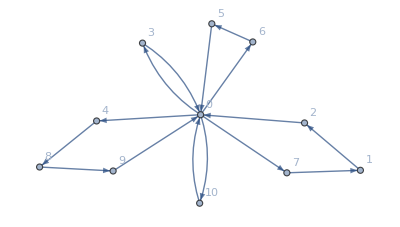

```mathematica
vert=Cases[sol[[;;(n+1)!/((n+1)-2)!]]*varsX,Except[0]];
Graph[#[[1]]->#[[2]]&/@vert,VertexLabels->"Name"]
```